# Local Optimization on the Gaussian manifold

This notebook is intended as a guide to using the optimization algorithm performing gradient descent over the manifold of pure bosonic or fermionic Gaussian states.

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<GaussianOptimization`
```

# The GaussianOptimization.m package and its functions

All functions included in the package, in alphabetical order:

```mathematica
?"GaussianOptimization`*"
```

## Optimization algorithm

```mathematica
?GOOptimize
```

For a more detailed explanation of the input arguments, see the guide to setting up a customization at the end of this document!

## Basic Tools and Fundamental definitions

Symplectic forms and Covariance matrices

For Bosonic states

```mathematica
?GOΩqpqp
```

```mathematica
?GOΩqqpp
```

```mathematica
?GOΩaabb
```

```mathematica
?GOΩabab
```

For Fermionic states

```mathematica
?GOGqpqp
```

```mathematica
?GOGqqpp
```

```mathematica
?GOGaabb
```

```mathematica
?GOGabab
```

Transforming between structures

```mathematica
?GOTransformGtoJ
```

```mathematica
?GOTransformΩtoJ
```

```mathematica
?GOTransformJtoG
```

```mathematica
?GOTransformJtoΩ
```

Basis Transformation matrices

We provide basis transformation matrices for transformations between four bases (note that b_i are the respective annihilation operators):
 (q_1,p_1,q_2,p_2,...) 	(q_1,q_2,...,p_1,p_2,...)	(a_1,b_1,a_2,b_2,...)	(a_1,a_2,...,b_1,b_2,...)

where we have defined:		a_i=1/(√2)(q_i+ⅈ p_i)  and   b_i=1/(√2)(q_i-ⅈ p_i)

Re-ordering

```mathematica
?GOqqppFROMqpqp
```

```mathematica
?GOqpqpFROMqqpp
```

```mathematica
?GOaabbFROMabab
```

```mathematica
?GOababFROMaabb
```

position / momentum → annihilation / creation operators

```mathematica
?GOababFROMqpqp
```

```mathematica
?GOaabbFROMqpqp
```

```mathematica
?GOababFROMqqpp
```

```mathematica
?GOaabbFROMqqpp
```

annihilation / creation operators → position / momentum

```mathematica
?GOqpqpFROMabab
```

```mathematica
?GOqqppFROMabab
```

```mathematica
?GOqpqpFROMaabb
```

```mathematica
?GOqqppFROMaabb
```

Lie algebra bases

All Lie algebra bases are generated in the basis  (q_1,p_1,q_2,p_2,...)  by convention

```mathematica
?GOLieBasisSp
GOLieBasisSp[2]//Dimensions
```

{10,4,4}

```mathematica
?GOLieBasisSpNoUN
GOLieBasisSpNoUN[2]//Dimensions
```

{6,4,4}

```mathematica
?GOLieBasisSpNoU1
```

```mathematica
?GOLieBasisSpMixing
GOLieBasisSpMixing[1,1]//Dimensions
```

{4,4,4}

```mathematica
?GOLieBasisSO
GOLieBasisSO[2]//Dimensions
```

{6,4,4}

```mathematica
?GOLieBasisEmpty
GOLieBasisEmpty[2]//Dimensions
```

{1,4,4}

We can also construct a compound Lie algebra basis for a system that is divided into two subsystems:

```mathematica
?GOLieBasisCompound
GOLieBasisCompound[{GOLieBasisEmpty[2],GOLieBasisSp[2],GOLieBasisEmpty[6]}]//Dimensions
```

{10,20,20}

Metrics for the symplectic and orthogonal manifolds

```mathematica
?GOMetricSp
```

GOMetricSp[K,J_0] generates the natural metric for the symplectic manifold with Lie basis K, for an initial state J_0

```mathematica
?GOMetricO
```

GOMetricO[K,J_0] generates the natural metric for the orthogonal manifold with Lie basis K

Generating random Transformations

```mathematica
?GORandomTransformation
```

GORandomTransformation[n,'Basis'] generates a random transformation in the Lie group with algebra 'Basis'

Tools for computational efficiency

```mathematica
?GOapproxExp
```

approxExp[ϵ,K]=(1 + ϵ/2 K)/(1 - ϵ/2 K) approximates MatrixExponential[ϵX]

```mathematica
?GOlogfunction
```

logfunction[x] takes value 0 when x=0 and log[x] otherwise

```mathematica
?GOConditionalLog
```

GOConditionalLog[x] calculates MatrixLog[x] by applying logfunction to the eigenvalues of x

```mathematica
?GOinvMSp
```

invMSp[m,'Mform'] inverts a symplectic matrix m in the basis Mform as m^-1=-ΩmΩ

## Applications implemented in GaussianOptimization.m

Purifications and the standard form

```mathematica
?GOExtractStdFormG
```

{rlist,Tra}=GOExtractStdFormG[G]
Returns the parameters for constructing the standard form of G (list of the r_i and the transformation matrix Tra that puts G into standard form

```mathematica
?GOExtractStdFormΩ
```

{rlist,Tra}=GOExtractStdFormΩ[Ω]
Returns the parameters for constructing the standard form of Ω (list of the r_i and the transformation matrix Tra that puts Ω into standard form

```mathematica
?GOPurifyStandardGBoson
```

G_sta=GOPurifyStandardGBoson[rlist,N,'Gform']
Constructs the bosonic purified state convariance matrix in the basis Gform with N degrees of freedom in the ancillary

```mathematica
?GOPurifyStandardJBoson
```

J_sta=GOPurifyStandardJBoson[rlist,N,'Jform']
Constructs the bosonic purified state complex structure in the basis Jform with N degrees of freedom in the ancillary

```mathematica
?GOPurifyStandardΩFermion
```

Ω_sta=GOPurifyStandardΩFermion[rlist,N,'Ωform']
Constructs the fermionic purified state convariance matrix in the basis Ωform with N degrees of freedom in the ancillary

```mathematica
?GOPurifyStandardJFermion
```

J_sta=GOPurifyStandardJFermion[rlist,N,'Jform']
Constructs the fermionic purified state complex structure in the basis Jform with N degrees of freedom in the ancillary

Entanglement of Purification

```mathematica
?GORestrictionAA
```

GORestrictionAA[{dimA1, dimB1, dimA2, dimB2}] generates the restriction function for use in calculating EoP for a system decomposed into degrees of freedom {dimA1, dimB1, dimA2, dimB2}

```mathematica
?GOEoPBos
```

GOEoPBos[Restriction] generates a function f[M,J_0] which calculates the bosonic EoP for the given restriction

```mathematica
?GOEoPgradBos
```

GOEoPgradBos[Restriction] generates a function df[M,J_0,K,G^-1] which calculates the gradient of the bosonic EoP for the given restriction with respect to the Lie algebra basis K

```mathematica
?GOEoPFerm
```

GOEoPBos[Restriction] generates a function f[M,J_0] which calculates the fermionic EoP for the given restriction

```mathematica
?GOEoPgradFerm
```

GOEoPgradFerm[Restriction] generates a function df[M,J_0,K,G^-1] which calculates the gradient of the fermionic EoP for the given restriction with respect to the Lie algebra basis K

Complexity of Purification

```mathematica
?GOCoPBos
```

GOCoPBos[J_T] generates a function f[M,J_R0] which calculates the bosonic CoP with respect to the given target state J_T

```mathematica
?GOCoPgradBos
```

GOCoPBos[J_T] generates a function df[M,J_R0,K,G^-1] which calculates the gradient of the bosonic CoP with respect to the given target state J_T and the Lie algebra basis K

```mathematica
?GOCoPFerm
```

GOCoPFerm[J_T] generates a function f[M,J_R0] which calculates the fermionic CoP with respect to the given target state J_T

```mathematica
?GOCoPgradFerm
```

GOCoPgradFerm[J_T] generates a function df[M,J_R0,K,G^-1] which calculates the gradient of the fermionic CoP with respect to the given target state J_T and the Lie algebra basis K

Energy of quadratic Hamiltonians

```mathematica
?GOenergyBos
```

GOenergyBos[h] generates an energy function f[M,J_0] for a bosonic quadratic Hamiltonian H=h_abξ^aξ^b

```mathematica
?GOenergygradBos
```

GOenergygradBos[h] generates an energy gradient function df[M,J_0,K] for a bosonic quadratic Hamiltonian H=h_abξ^aξ^b with respect to the Lie algebra basis K

```mathematica
?GOenergyFerm
```

GOenergyFerm[h] generates an energy function f[M,J_0] for a fermionic quadratic Hamiltonian H=h_abξ^aξ^b

```mathematica
?GOenergygradFerm
```

GOenergygradBos[h] generates an energy gradient function df[M,J_0,K] for a fermionic quadratic Hamiltonian H=h_abξ^aξ^b with respect to the Lie algebra basis K

# Selected examples: EoP and CoP

## Bosonic Entanglement of Purification (EoP)

```mathematica
mass=.1;
latticespacing=1.;
sites=100;
dimA1=3;
dimB1=3;
dimA2=3;
dimB2=3;
sep=0;
```

#### 0. Initialize definitions: Functions to generate the initial covariance matrices for a lattice free scalar field theory

```mathematica
FourierMatrixElement[N_]:=Function[{k,x},Exp[I 2 Pi x k /N]/Sqrt[N]];
DispersionRelation[m_,N_,l_]:=Function[{k},Sqrt[m^2+4/l^2  (Sin[Pi k/N])^2]];
```

```mathematica
FT[n_]:=Module[{f,pos,val},
f=FourierMatrixElement[n];
pos=Table[{x,k},{k,n},{x,n}]//Flatten[#,1]&;
val=Table[f[k,x]//N,{k,n},{x,n}]//Flatten[#,1]&;
SparseArray[pos->val]];
```

```mathematica
Diag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[ω[k],{k,n}]]];
```

```mathematica
invDiag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[1/ω[k],{k,n}]]];
```

```mathematica
CM[N_,m_,l_]:=Module[{F,D,invD,G,Tr},
F=FT[N];D=Diag[m,N,l]; invD=invDiag[m,N,l];
G=ArrayFlatten[({{F.D.ConjugateTranspose[F], 0}, {0, F.invD.ConjugateTranspose[F]}})]//Chop//SparseArray];
```

```mathematica
partialCM[N_,m_,l_,d_,dim1_,dim2_]:=
Module[{dim, halfdim, bigCM, indices1, indices2,indices, partialCM, Tr},

bigCM=CM[N,m,l];
dim=Length[bigCM]; halfdim=dim/2;

indices1=Thread[{Table[x,{x,dim1}],Table[x+halfdim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+halfdim,{x,dim2}]}]//Flatten[#,1]&;

indices=Join[indices1,indices2];

partialCM=bigCM[[indices,indices]]];
```

#### 1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In the example below, the mixed state is obtained for a system with total number of lattice sites 100 with 3 sites per subsystem in the initial system, mass term 0.1, lattice spacing 1, 
and no lattice sites separating the subsystems.

```mathematica
CM0=partialCM[100,mass,latticespacing,sep,dimA1,dimB1]; CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

#### 2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0];
J0=GOPurifyStandardJBoson[rlist,dimA2+dimB2,"qpqp"];
```

#### 4. Define the problem-specific input arguments

```mathematica
Restriction=GORestrictionAA[{dimA1,dimB1,dimA2,dimB2}];
function=GOEoPBos[Restriction];
gradient=GOEoPgradBos[Restriction];
ProblemSpecific={function,gradient};
```

#### 5. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSp[dimA2+dimB2]}];

M0=ArrayFlatten[{{Inverse[MTra],0},{0,IdentityMatrix[2dimA2+2dimB2]}}]//SparseArray;
M0List=Table[MatrixExp[RandomReal[{0,0.3},Length[LieBasis]].LieBasis].M0,{i,50}];

newM[m_,s_,x_]:=m.GOapproxExp[s,x];

metric=GOMetricSp[LieBasis,J0]; (*not needed, from older version for comparison) *)
geometry=GOGeometryConst[LieBasis,J0,+1];
```

```mathematica
SystemSpecific={J0,M0List,LieBasis,{None,IdentityMatrix[Length[LieBasis]]},newM};
```

#### 6. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-12; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

#### 7. Run the Optimization

```mathematica
{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

{1.41899,1.28093,1.25467,1.33858,1.39404,1.40642,1.60001,1.17451,1.40387,1.33218,1.24111,1.47334,1.38959,1.44568,1.34935,1.28378,1.34409,1.60911,1.52555,1.2877,1.05271,1.5163,1.55804,1.24435,1.25644,1.27553,1.30018,1.43016,1.54492,1.33648,1.56512,1.42118,1.32031,1.43772,1.42019,1.33118,1.34498,1.69386,1.47855,1.36831,1.5524,1.37093,1.36566,1.49191,1.38008,1.2208,1.31432,1.59555,1.45569,1.63427}

$Aborted

#### 8. Evaluate the result

Time taken: 3.9375 seconds

Final value: 1.42343

Number of iterations: 6

Number of total corrections: 395

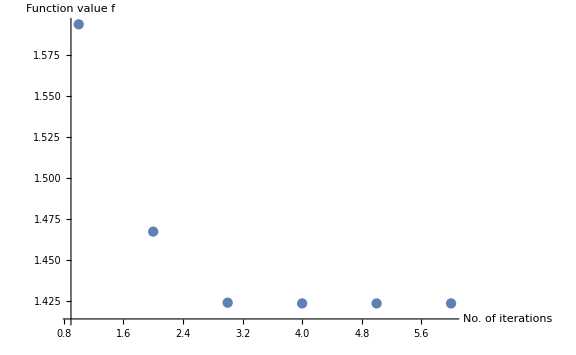

```mathematica
Print["Time taken: ",Time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦4⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

## Bosonic Complexity of Purification (CoP)

```mathematica
mass=.1;
latticespacing=1.;
sites=100;
dimA1=3;
dimB1=3;
dimPur=dimA1+dimB1;
sep=0;
```

#### 0. Initialize definitions: Functions to generate the initial covariance matrices for a lattice free scalar field theory

```mathematica
FourierMatrixElement[N_]:=Function[{k,x},Exp[I 2 Pi x k /N]/Sqrt[N]];
DispersionRelation[m_,N_,l_]:=Function[{k},Sqrt[m^2+4/l^2  (Sin[Pi k/N])^2]];
```

```mathematica
FT[n_]:=Module[{f,pos,val},
f=FourierMatrixElement[n];
pos=Table[{x,k},{k,n},{x,n}]//Flatten[#,1]&;
val=Table[f[k,x]//N,{k,n},{x,n}]//Flatten[#,1]&;
SparseArray[pos->val]];
```

```mathematica
Diag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[ω[k],{k,n}]]];
```

```mathematica
invDiag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[1/ω[k],{k,n}]]];
```

```mathematica
CM[N_,m_,l_]:=Module[{F,D,invD,G,Tr},
F=FT[N];D=Diag[m,N,l]; invD=invDiag[m,N,l];
G=ArrayFlatten[({{F.D.ConjugateTranspose[F], 0}, {0, F.invD.ConjugateTranspose[F]}})]//Chop//SparseArray];
```

```mathematica
partialCM[N_,m_,l_,d_,dim1_,dim2_]:=
Module[{dim, halfdim, bigCM, indices1, indices2,indices, partialCM, Tr},

bigCM=CM[N,m,l];
dim=Length[bigCM]; halfdim=dim/2;

indices1=Thread[{Table[x,{x,dim1}],Table[x+halfdim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+halfdim,{x,dim2}]}]//Flatten[#,1]&;

indices=Join[indices1,indices2];

partialCM=bigCM[[indices,indices]]];
```

#### 1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In the example below, the mixed state is obtained for a system with total number of lattice sites 100 with 3 sites per subsystem in the initial system, mass term 0.1, lattice spacing 1, 
and no lattice sites separating the subsystems.

```mathematica
CM0=partialCM[100,mass,latticespacing,sep,dimA1,dimB1]; CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

#### 2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0];
JT=GOPurifyStandardJBoson[rlist,dimPur,"qpqp"];
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
```

#### 4. Define the problem-specific input arguments

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
ProblemSpecific={function,gradient};
```

#### 5. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];

M0=ArrayFlatten[{{Inverse[MTra],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray;
M0List=Table[MatrixExp[RandomReal[{0,0.1},Length[LieBasis]].LieBasis].M0,{i,50}];

newM[m_,s_,x_]:=m.GOapproxExp[s,x];

metric=GOMetricSp[LieBasis,JR0]; (*not needed, from older version for comparison) *)
geometry=GOGeometryConst[LieBasis,JR0,+1];


SystemSpecific={JR0,M0List,LieBasis,geometry,newM};
```

#### 6. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

#### 7. Run the Optimization

```mathematica
{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

{1.12332,1.09607,1.10722,1.10319,1.11093,1.09719,1.0877,1.0951,1.10274,1.10026,1.1203,1.10886,1.09081,1.09582,1.09772,1.11804,1.11464,1.10848,1.11031,1.08198,1.094,1.09097,1.10653,1.10587,1.09945,1.10772,1.1104,1.10604,1.12138,1.1056,1.10009,1.10926,1.11641,1.10362,1.1038,1.11217,1.08823,1.11769,1.11224,1.1081,1.11818,1.09929,1.09673,1.10279,1.09695,1.10409,1.08757,1.10043,1.09855,1.10903}

Reason for termination: Function value tolerance reached

#### 8. Evaluate the result

Time taken: 7.26563 seconds

Final value: 1.0354

Number of iterations: 6

Number of total corrections: 0

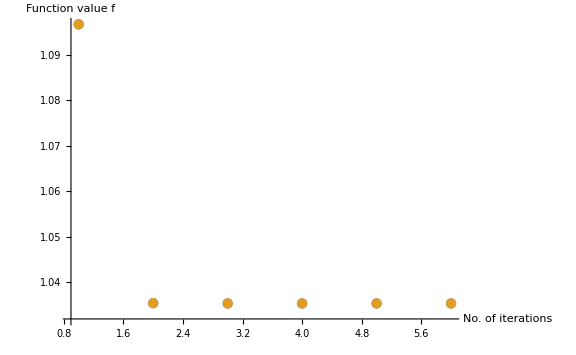

```mathematica
Print["Time taken: ",Time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦4⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

## Fermionic Entanglement of Purification (EoP)

```mathematica
NN=30; (* Total number lattice sites *)
J=1;h=.5;γ=.5; (* XY model parameter*)
dimA1=2; dimB1=2; (* dofs of chosen subystems *)
d=3; (* distance subsystems *)
dimA2=dimA1;dimB2= dimB1;(* purifying dofs, dimA2+dimB2 ≥ dimA1+dimB1 *)
```

#### 0. Initialize definitions: Functions to generate the initial covariance matrices for the XY model

```mathematica
ϵ[k_]=√(h^2+2h J Cos[k]+J^2+(γ^2-1)J^2 Sin[k]^2);
a[k_]=-J Cos[k]-h;
b[k_]=γ J Sin[k];
u[k_]=(ϵ[k]+a[k])/(√(2ϵ[k](ϵ[k]+a[k])));
v[k_]=(ⅈ b[k])/(√(2ϵ[k](ϵ[k]+a[k])));
```

#### 1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In this case we are generating a covariance matrix for a system with a total of 10 lattice sites and partitioning it into two adjacent subsystems containing 2 lattice sites each.

```mathematica
u[0]=0;v[0]=ⅈ;u[π]=1;v[π]=0;
Ωblock=1/NN Table[Sum[(Abs[v[2π k/NN]]^2-Abs[u[2π k/NN]]^2//N)Cos[2π k(j-l)/NN]+2Im[v[2π k/NN]u[2π k/NN]]Sin[2π k(j-l)/NN],{k,0,NN-1}],{j,1,NN},{l,1,NN}];
ΩΩ=ArrayFlatten[({{0, Ωblock}, {-Transpose[Ωblock], 0}})];JJ=ΩΩ;
```

```mathematica
dim1=dimA1;dim2=dimB1;dim=NN;
indices1=Thread[{Table[x,{x,dim1}],Table[x+dim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+dim,{x,dim2}]}]//Flatten[#,1]&;
indices=Join[indices1,indices2];

Tran=GOqpqpFROMqqpp[dim]; ΩΩqpqp=Tran.ΩΩ.Transpose[Tran];
Ω0=ΩΩqpqp[[indices,indices]]; Ω0//MatrixForm
```

(0. | 0. | 0.296657 | 0.0000895099 | -0.0392786 | 5.8775×10^-6 | 0. | 0.
0. | 0. | 0.0000895099 | 0.296657 | 5.8775×10^-6 | -0.0392786 | 0. | 0.
-0.296657 | -0.0000895099 | 0. | 0. | 0. | 0. | -0.0196949 | -0.0000301449
-0.0000895099 | -0.296657 | 0. | 0. | 0. | 0. | -0.0000301449 | -0.0196949
0.0392786 | -5.8775×10^-6 | 0. | 0. | 0. | 0. | -0.88587 | 0.0000154959
-5.8775×10^-6 | 0.0392786 | 0. | 0. | 0. | 0. | 0.0000154959 | -0.88587
0. | 0. | 0.0196949 | 0.0000301449 | 0.88587 | -0.0000154959 | 0. | 0.
0. | 0. | 0.0000301449 | 0.0196949 | -0.0000154959 | 0.88587 | 0. | 0.)

#### 2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormΩ[Ω0];
MTra//Dimensions
```

{8,8}

```mathematica
J0=GOPurifyStandardJFermion[rlist,dimA2+dimB2,"qpqp"];
rlist
```

{0.24023,0.240263,0.634456,0.634551}

```mathematica
Eigenvalues[Ω0]//Im
```

{0.886783,-0.886783,0.886752,-0.886752,0.29732,-0.29732,0.297138,-0.297138}

#### 4. Define the problem-specific input arguments

```mathematica
Restriction=GORestrictionAA[{dimA1,dimB1,dimA2,dimB2}];
function=GOEoPFerm[Restriction]; gradient=GOEoPgradFerm[Restriction];
ProblemSpecific={function,gradient};
```

#### 5. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSO[dimA2+dimB2]}];
M0=ArrayFlatten[{{Inverse[MTra],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray;
M0List=Table[MatrixExp[RandomReal[{0,0.1},Length[LieBasis]].LieBasis].M0,{i,50}];

newM[m_,s_,x_]:=m.GOapproxExp[s,x];

metric=GOMetricO[LieBasis]; (*not needed, from older version for comparison) *)
geometry=GOGeometryConst[LieBasis,J0,-1];

SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

#### 6. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

#### 7. Run the Optimization

```mathematica
{time,Result}=AbsoluteTiming[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

{1.7206,1.72211,1.71708,1.71984,1.71648,1.71954,1.72581,1.72127,1.7168,1.72619,1.71871,1.72116,1.72053,1.72347,1.72212,1.72215,1.71774,1.7151,1.71386,1.71784,1.72188,1.72386,1.71854,1.71947,1.71875,1.71353,1.71487,1.71946,1.72059,1.71446,1.71828,1.71688,1.71312,1.72428,1.71442,1.71612,1.72088,1.72525,1.72021,1.71492,1.72095,1.71846,1.7225,1.71863,1.72278,1.72057,1.71982,1.72058,1.72669,1.72619}

Reason for termination: Gradient norm tolerance reached

#### 8. Evaluate the result

Time taken: 0.1875 seconds

Final value: 0.00723634

Number of iterations: 71

Number of total corrections: 0

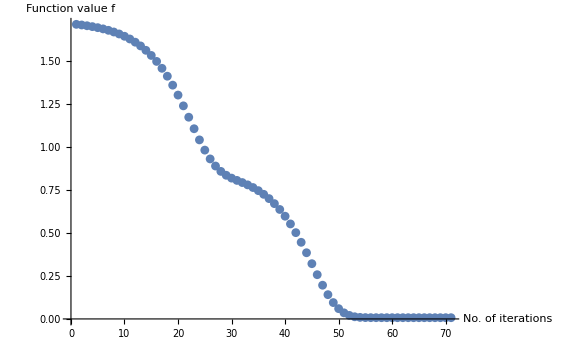

```mathematica
Print["Time taken: ",Time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦4⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

## Fermionic Complexity of Purification (CoP)

```mathematica
NN=30; (* Total number lattice sites *)
J=1;h=.5;γ=.5; (* XY model parameter*)
dimA1=2; dimB1=2; (* dofs of chosen subystems *)
d=0; (* distance subsystems *)
dimPur=dimA1+dimB1;(* purifying dofs, dimPur ≥ dimA1+dimB1 *)
JR0=GOTransformΩtoJ[GOΩqpqp[dimA1+dimB1+dimPur],"qpqp","qpqp"]; (* reference state*)
```

#### 0. Initialize definitions: Functions to generate the initial covariance matrices for the XY model

```mathematica
ϵ[k_]=√(h^2+2h J Cos[k]+J^2+(γ^2-1)J^2 Sin[k]^2);
a[k_]=-J Cos[k]-h;
b[k_]=γ J Sin[k];
u[k_]=(ϵ[k]+a[k])/(√(2ϵ[k](ϵ[k]+a[k])));
v[k_]=(ⅈ b[k])/(√(2ϵ[k](ϵ[k]+a[k])));
```

#### 1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In this case we are generating a covariance matrix for a system with a total of 10 lattice sites and partitioning it into two adjacent subsystems containing 2 lattice sites each.

```mathematica
u[0]=0;v[0]=ⅈ;u[π]=1;v[π]=0;
Ωblock=1/NN Table[Sum[(Abs[v[2π k/NN]]^2-Abs[u[2π k/NN]]^2//N)Cos[2π k(j-l)/NN]+2Im[v[2π k/NN]u[2π k/NN]]Sin[2π k(j-l)/NN],{k,0,NN-1}],{j,1,NN},{l,1,NN}];
ΩΩ=ArrayFlatten[({{0, Ωblock}, {-Transpose[Ωblock], 0}})];JJ=ΩΩ;
```

```mathematica
dim1=dimA1;dim2=dimB1;dim=NN;
indices1=Thread[{Table[x,{x,dim1}],Table[x+dim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+dim,{x,dim2}]}]//Flatten[#,1]&;
indices=Join[indices1,indices2];

Tran=GOqpqpFROMqqpp[dim]; ΩΩqpqp=Tran.ΩΩ.Transpose[Tran];
Ω0=ΩΩqpqp[[indices,indices]]; Ω0//MatrixForm
```

(0. | 0. | 0.296657 | 0.0000895099 | 0. | 0. | 0.123704 | -0.000139593
0. | 0. | 0.0000895099 | 0.296657 | 0. | 0. | -0.000139593 | 0.123704
-0.296657 | -0.0000895099 | 0. | 0. | -0.88587 | 0.0000154959 | 0. | 0.
-0.0000895099 | -0.296657 | 0. | 0. | 0.0000154959 | -0.88587 | 0. | 0.
0. | 0. | 0.88587 | -0.0000154959 | 0. | 0. | 0.296657 | 0.0000895099
0. | 0. | -0.0000154959 | 0.88587 | 0. | 0. | 0.0000895099 | 0.296657
-0.123704 | 0.000139593 | 0. | 0. | -0.296657 | -0.0000895099 | 0. | 0.
0.000139593 | -0.123704 | 0. | 0. | -0.0000895099 | -0.296657 | 0. | 0.)

#### 2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormΩ[Ω0];
JT=GOPurifyStandardJFermion[rlist,dimPur,"qpqp"];
```

#### 4. Define the problem-specific input arguments

```mathematica
function=GOCoPFerm[JT]; gradient=GOCoPgradFerm[JT];
ProblemSpecific={function,gradient};
```

#### 5. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSO[dimPur]}];
M0=ArrayFlatten[{{Inverse[MTra],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray;
M0List=Table[MatrixExp[RandomReal[{0,.1},Length[LieBasis]].LieBasis].M0,{i,50}];

newM[m_,s_,x_]:=m.GOapproxExp[s,x];

metric=GOMetricO[LieBasis]; (*not needed, from older version for comparison) *)
geometry=GOGeometryConst[LieBasis,JR0,-1];

SystemSpecific={JR0,M0List,LieBasis,geometry,newM};
```

#### 6. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

#### 7. Run the Optimization

```mathematica
{time,Result}=AbsoluteTiming[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

{1.7313,1.7284,1.72555,1.72504,1.73428,1.72226,1.7269,1.73166,1.73205,1.72431,1.72773,1.7218,1.72637,1.73115,1.72364,1.72526,1.73081,1.72996,1.73132,1.72477,1.73043,1.72241,1.72596,1.72043,1.73372,1.72126,1.72755,1.728,1.73267,1.72072,1.72676,1.72649,1.73018,1.72703,1.73261,1.72961,1.72188,1.72854,1.72732,1.72858,1.72922,1.73231,1.72924,1.73453,1.72719,1.72471,1.73184,1.73386,1.7266,1.73091}

Reason for termination: Function value tolerance reached

#### 8. Evaluate the result

Time taken: 0.1875 seconds

Final value: 1.49163

Number of iterations: 30

Number of total corrections: 0

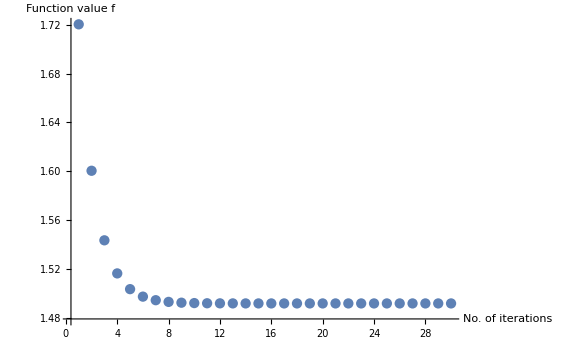

```mathematica
Print["Time taken: ",Time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦4⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

# Setting up a custom optimization

This section is intended as a concise guide to applying the GaussianOptimization.m package and its functions to an arbitrary optimization problem.
As shown in the function description for GOOptimize above, the input arguments for the optimization can be grouped into three categories:

#### 1. Problem-Specific input arguments

These are the arguments that are related specifically to the physical quantity under investigation. They are:

f -- The function to be optimized (must be a function of the transformation M, and the initial state complex structure J_0)

df -- The gradient associated with the function to be optimized (must be a function of the transformation M, the initial state complex structure J_0, the Lie algebra basis K, and the inverse metric G^-1)

#### 2. System-Specific input arguments

These are the arguments that are related to the geometry of the manifold over which the optimization is conducted, including also the points in the manifold, from which the optimization is initialized. Changing the system-specific arguments while keeping all other arguments the same means changing only the landscape on which the gradient descent is performed.
Import note: All system specific input arguments must be in the basis (q_1,p_1,q_2,p_2,...)!

J_0 -- The initial state complex structure

{M_0} -- A list of the initial transformations to be applied to J_0 (together with J_0, these transformations parametrize the starting points for the gradient descent)

{K_i} -- The Lie algebra basis

G^-1 -- The inverse natural metric

These input arguments are key to the theory underlying this optimization algorithm: The inverse natural metric is used by the gradient function to calculate a consistent value for the gradient vector, independent of basis choice. More importantly, it should be noted that any constraints on the optimization are implemented by restricting the Lie algebra basis to those elements K_i which generate transformations that only transform within the restricted class of states of interest.

#### 3. Procedure-Specific input arguments

These input arguments specify parameters relating to the numerical implementation of the optimization. Firstly, this includes three stopping criteria:

tol_F -- Tolerance on the function values (stopping criterion: (F_(n+1)-F_n)/F_(n+1)<tol_F)

tol_F -- Tolerance on the function values (stopping criterion: (F_(n+1)-F_n)/F_(n+1)<tol_F)

lim_iter  -- Limit on the number of iterations (stopping criterion: n>lim_iter; the default value of this argument is ∞)

The algorithm is terminated as soon as any of the three stopping criteria is violated by all of the trajectories still under consideration.

Secondly, the procedure-specific input arguments include the sub-routine for correcting the step size in the case where F_(n+1)>F_ninitially. This subroutine must be of function of the current step size only, which returns only the new step size. The most rudimentary implementation, used in the examples above, is simply step(ϵ)=ϵ/2.

Thirdly, the input arguments include optional arguments for debugging modes of the algorithm. In particular, at the moment there is only one such optional parameter, which tales either True or False as values, where False corresponds to running the algorithm in its most efficient version, without debugging.

track all trajectories? -- This completes the full optimization procedure for all starting points, rather than only the most promising trajectories